# 2. Multiple Integrals

Create a table of the five fundamental functions x^n, sin (x), cos (x), exp (x), and ln (x). List both their derivatives and their anti-derivatives. Include in your table at least one other example. Use the Mathematica functions D and Integrate to verify these.

```mathematica
D[{x^n,Sin[x],Cos[x],Exp[x],Log[x],Tan[x]},x]
Integrate[{x^n,Sin[x],Cos[x],Exp[x],Log[x],Tan[x]},x]
```

{n x^(-1+n),Cos[x],-Sin[x],ⅇ^x,1/x,Sec[x]^2}

{x^(1+n)/(1+n),-Cos[x],Sin[x],ⅇ^x,-x+x Log[x],-Log[Cos[x]]}

Use your table of fundamental functions and these properties to evaluate the derivative and integral of 4 x^2 + 3 x^2- 5x + 4. Verify your answer using the Mathematica functions D and Integrate.

```mathematica
D[4*x^2 + 3*x^2 - 5*x + 4,x]
Integrate[4*x^2 + 3*x^2 - 5*x + 4,x]
```

-5+14 x

4 x-(5 x^2)/2+(7 x^3)/3

Use your table of fundamental functions and the chain rule to determine the derivative of (x^3 - 1)^100. Verify your answer using the Mathematica function D.

```mathematica
D[(x^3-1)^100,x]
```

300 x^2 (-1+x^3)^99

Use your table of fundamental functions and the substitution
rule to evaluate ∫_0^4 √(2x+1)ⅆx. Verify your answer using the Mathematica function Integrate.

```mathematica
Integrate[Sqrt[2*x+1],{x,0,4}]
```

26/3

Use your table of fundamental functions and the product rule to determine the derivative of √x(1-x). Verify your answer using the Mathematica function D.

```mathematica
D[Sqrt[x]*(1-x),x]
Simplify[%]
```

(1-x)/(2 √x)-√x

(1-3 x)/(2 √x)

Use your table of fundamental functions and integration by parts to determine ∫_1^2 x e^-x ⅆx. Verify your answer using the Mathematica function Integrate.

```mathematica
Integrate[x*Exp[-x],{x,1,2}]
N[%]
```

(-3+2 ⅇ)/ⅇ^2

0.329753

Find the derivative and integral of the following functions, and verify your answers using the Mathematica functions D and Integrate.

A e^(k t)

```mathematica
D[A*Exp[k*t],t]
Integrate[A*Exp[k*t],t]
```

A ⅇ^(k t) k

(A ⅇ^(k t))/k

f(x) = m x + b

```mathematica
D[m*x+b,x]
Integrate[m*x+b,x]
```

m

b x+(m x^2)/2

f(x) = a x^n + b

```mathematica
D[a*x^n+b,x]
Integrate[a*x^n+b,x]
```

a n x^(-1+n)

b x+(a x^(1+n))/(1+n)

f(t) = A sin(ω t + ϕ)

```mathematica
D[A*Sin[omega*t+phi],t]
Simplify[Integrate[A*Sin[omega*t+phi],t]]
```

A omega Cos[phi+omega t]

-(A Cos[phi+omega t])/omega

f(x) = g (x - h)^2 + k

```mathematica
D[g*(x-h)^2+k,x]
Simplify[Integrate[g*(x-h)^2+k,x]]
```

2 g (-h+x)

k x+1/3 g x (3 h^2-3 h x+x^2)

Consider the five fundamental functions x^n, sin(x), cos(x), e^x, ln(x). Find the area under their curves between x = 0 and x = 1. Use the Mathematica function Integrate to verify your calculations.

```mathematica
Integrate[{x^n,Sin[x],Cos[x],Exp[x],Log[x]},{x,0,1}]
```

{ConditionalExpression[1/(1+n),Re[n]>-1],1-Cos[1],Sin[1],-1+ⅇ,-1}

Consider the parabola defined by y = x^2. Propose an integral that would determine the area enclosed on the top by y = d, d > 0, on the bottom by y = x^2, on the left by x = 0, and on the right by the intersection of the top and bottom functions. Evaluate it using Mathematica. This region is illustrated in Figure 4.

We have a little preliminary work to do to find the intersection of the two curves. We seek the value of x where x^2= d, which corresponds to x = √d. We then integrate the difference between the two functions between x = 0 and x = √d.

```mathematica
Integrate[d-x^2,{x,0,Sqrt[d]}]
```

(2 d^(3/2))/3

Sketch the regions of integration and compute the area of the enclosed region by evaluating the double integral. Verify your answer using the Mathematica functions RegionPlot and Integrate.

∫_0^1 ∫_0^x ⅆyⅆx

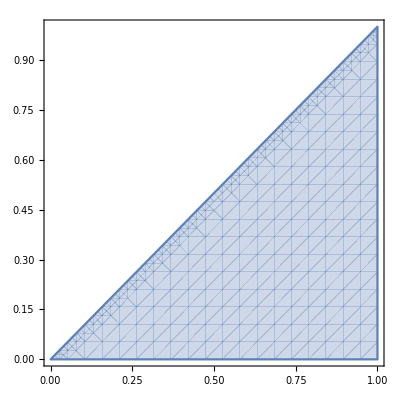

1/2

```mathematica
RegionPlot[0<y<x&&0 < x< 1,{x,0,1},{y,0,1}]
Integrate[1,{x,0,1},{y,0,x}]
```

∫_1^2 ∫_0^lnx ⅆyⅆx

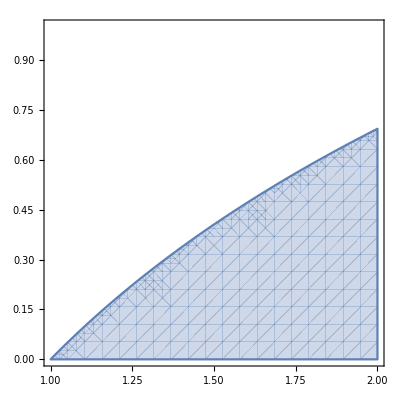

-1+Log[4]

0.386294

```mathematica
RegionPlot[0<y<Log[x]&& 1<x<2,{x,1,2},{y,0,1}]
Integrate[1,{x,1,2},{y,0,Log[x]}]
N[%]
```

Sketch the regions of integration and compute the area of the enclosed region by evaluating the double integral. Verify your answer using the Mathematica functions RegionPlot and Integrate.

∫_0^1 ∫_y^(2-y) ⅆxⅆy

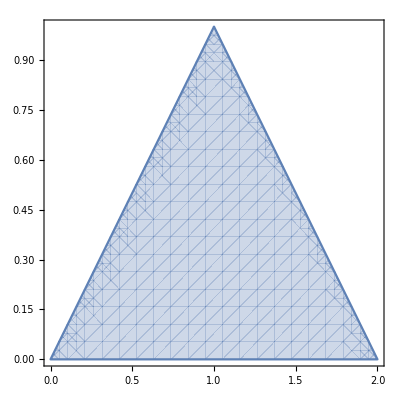

1

```mathematica
RegionPlot[y<x<2-y&&0<y<1,{x,0,2},{y,0,1}]
Integrate[1,{y,0,1},{x,y,2-y}]
```

∫_0^1 ∫_y^(exp(y)) ⅆxⅆy

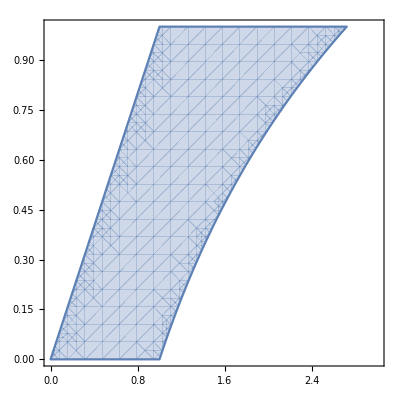

-3/2+ⅇ

1.21828

```mathematica
RegionPlot[y<x<Exp[y]&&0<y<1,{x,0,3},{y,0,1}]
Integrate[1,{y,0,1},{x,y,Exp[y]}]
N[%]
```

Repeat Exercises 10 and 11, but change the order of integration. The hard part is redefining the limits of integration.

The best way to change the order of integration is to use the image of the shape, imagine partitioning it into rectangles vertically and horizontally, and the define the appropriate limits. For each question we will write down the equivalent double integral and then use Integral to compute the value. We will show the result from both orders for easy of reading.

∫_0^1 ∫_0^x ⅆyⅆx =∫_0^1 ∫_y^1 ⅆxⅆy

```mathematica
Integrate[1,{x,0,1},{y,0,x}]
Integrate[1,{y,0,1},{x,y,1}]
```

1/2

1/2

∫_1^2 ∫_0^lnx ⅆyⅆx =∫_0^ln2 ∫_(exp(y))^2 ⅆxⅆy

```mathematica
Integrate[1,{x,1,2},{y,0,Log[x]}]
Integrate[1,{y,0,Log[2]},{x,Exp[y],2}]
```

-1+Log[4]

-1+Log[4]

∫_0^1 ∫_y^(2-y) ⅆxⅆy =∫_0^1 ∫_0^x ⅆyⅆx + ∫_1^2 ∫_0^(2-x) ⅆyⅆx

```mathematica
Integrate[1,{y,0,1},{x,y,2-y}]
Integrate[1,{x,0,1},{y,0,x}]+Integrate[1,{x,1,2},{y,0,2-x}]
```

1

1

∫_0^1 ∫_y^(exp(y)) ⅆxⅆy = ∫_0^1 ∫_0^x ⅆyⅆx + ∫_1^e ∫_lnx^1 ⅆyⅆx

```mathematica
Integrate[1,{y,0,1},{x,y,Exp[y]}]
Integrate[1,{x,0,1},{y,0,x}]+Integrate[1,{x,1,Exp[1]},{y,Log[x],1}]
```

-3/2+ⅇ

-3/2+ⅇ

Sketch the following regions of integration in the plane, and evaluate the double integral. Verify your results using the Mathematica functions RegionPlot and Integrate.

∫∫(4y)/(x^3+ 2)ⅆA = ∫_1^2 ∫_0^(2x) (4y)/(x^3+ 2)ⅆyⅆx

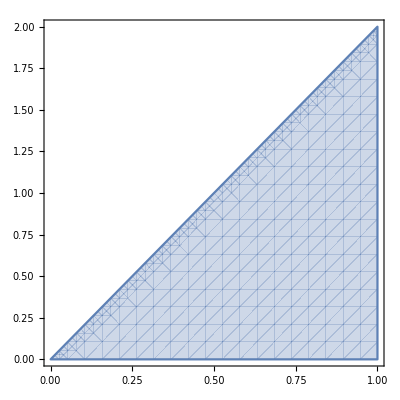

8/3 Log[3/2]

1.08124

```mathematica
RegionPlot[0<y<2*x&&0<x<1,{x,0,1},{y,0,2}]
Integrate[4*y/(x^3+2),{x,0,1},{y,0,2*x}]
N[%]
```

∫∫x cos yⅆA = ∫_0^1 ∫_0^(x^2) x cos yⅆyⅆx

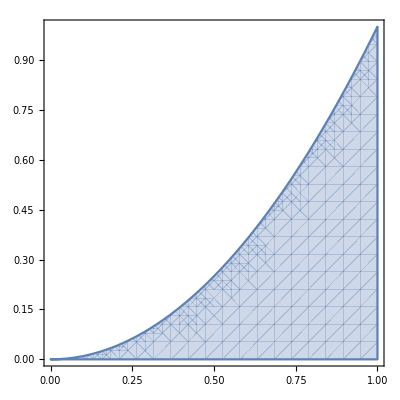

Sin[1/2]^2

0.229849

```mathematica
RegionPlot[0<y<x^2&&0<x<1,{x,0,1},{y,0,1}]
Integrate[x*Cos[y],{x,0,1},{y,0,x^2}]
N[%]
```

Use RegionPlot and Integrate to find the total mass and center of mass of the 1 cm thin aluminum plate bounded by the parabola y = x^2, y = 10, x = 0. Assume x and y are measured in centimeters.

A quick search on the internet reveals that the density of typical aluminum is 2.7 grams per cubic centimeter. The 1 cm thick plate therefore has an area density of 2.7 grams per square centimeter. The calculation below shows that the total mass of the plate is 56.9 grams, and the center of mass is (1.19,6), which appears to be correct.

56.921

1.18585

6.

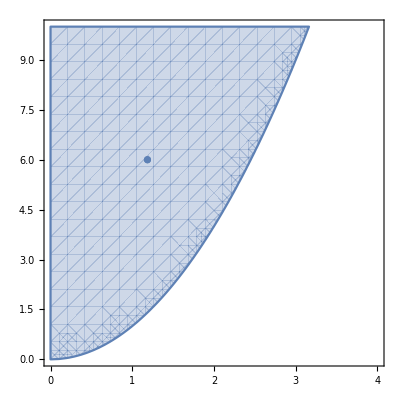

```mathematica
mass = Integrate[2.7,{y,0,10},{x,0,Sqrt[y]}]
xcom = Integrate[2.7*x,{y,0,10},{x,0,Sqrt[y]}]/mass
ycom = Integrate[2.7*y,{y,0,10},{x,0,Sqrt[y]}]/mass
Show[RegionPlot[x^2<y<10&&x>0,{x,0,4},{y,0,10}],ListPlot[{{xcom,ycom}}]]
```